```mathematica
SetDirectory["C:\\Chaozhi\\Mathematica Packages"]
Get["MagicGeneDropping`"]
SetDirectory[NotebookDirectory[]]
```

C:\Chaozhi\Mathematica Packages

C:\Chaozhi\Workspace\JuliaWorkspace\Workspace_RABBIT\RABBIT\MagicReconstruct\examples

```mathematica
(*****************************************************************************************************************)
```

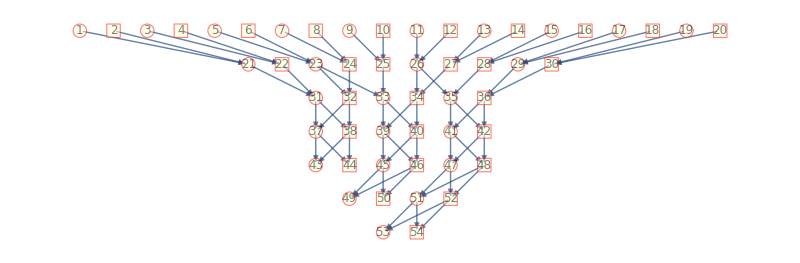

```mathematica
nFounder=8;
isOogamy=True;
pedigreels = Table[
mateScheme=Join[Table["Pairing",{2}],Table["Sibling",{1+i}]];
pedigree=simPedigree[nFounder,isOogamy,mateScheme];
pedigree,{i,3}];
Do[
oldmemls=pedigreels[[i]][[2;;,2]];
lastmem = oldmemls[[-1]];
memls=pedigreels[[i+1]][[2;;,2]];
newmemls = Range[lastmem+1,lastmem+Length[memls]];
newmemls[[{1,2,nFounder+1}]]=oldmemls[[{nFounder-3,nFounder-2,nFounder+nFounder/2-1}]];
pedigreels[[i+1]][[2;;,{2,4}]]=pedigreels[[i+1]][[2;;,{2,4}]]/.Thread[memls ->newmemls];
0,{i,2}];
ls=DeleteDuplicates[SortBy[Flatten[pedigreels[[All,2;;]],1],#[[;;2]]&]];
newped=Join[pedigreels[[1,{1}]],ls];
newped[[2;;,{2,4}]]=newped[[2;;,{2,4}]]/.Thread[newped[[2;;,2]]->Range[Length[newped]-1]];
pedigreePlot[newped,ImageSize->800]
```

```mathematica
newnf = Count[newped[[2;;,-1]],{0,0}];
subpopsize=10
memls = {73,74,79,80,83,84}-30
(*memls={35,36}*)
memls = Flatten[Table[#,{subpopsize}]&/@memls];
offls = Table["Offspring"<>ToString[i],{i,Length[memls]}];
funcode=Table[Range[newnf],{Length[offls]}];
sampleinfo = Join[{{"offspring","member","funcode"}},Transpose[{offls,memls,funcode}]];
sampleinfo[[;;;;50]]//MatrixForm
```

10

{43,44,49,50,53,54}

(offspring | member | funcode
Offspring50 | 53 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20})

```mathematica
pedinfo=mergePedigreeInfor[newped,sampleinfo];
(*Export["CC3_pedinfo.csv",pedinfo]*)
res=Transpose[{newped[[All,2]],newped[[All,4,1]],newped[[All,4,2]],newped[[All,3]]/.{1->"female",2->"male"}}];
res[[;;10]]//MatrixForm
Export["CC3_ped.csv",res]
```

CC3_pedinfo.csv

(MemberID | MotherID | FatherID | Female=1/Male=2/Hermaphrodite=0
1 | 0 | 0 | female
2 | 0 | 0 | male
3 | 0 | 0 | female
4 | 0 | 0 | male
5 | 0 | 0 | female
6 | 0 | 0 | male
7 | 0 | 0 | female
8 | 0 | 0 | male
9 | 0 | 0 | female)

CC3_ped.csv